```mathematica
e = 0;
τ=0;
psi0=0;
μ =3.9877848 10^14;
Mp=1000;
rc=6870000;
l=50000;
period = 2 π √(a^3/μ);
ranget=period*5;




psiQ =τ Cos[α[t]] Cos[γ[t]] ;
alphaQ =τ Sin[γ[t]];
  alphadsh0 = 0;
psidsh0 = 0;
r0 = a (1-e);
rdsh0 = 0;

θ[t]= √(μ/rc^3)t;
θ'[t]= √(μ/rc^3);
θ''[t]=0;

(*Position vectors and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc Cos[θ[t]]}, {rc Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});

Subscript[T, lin]=1/2 (2*Mp) (Transpose[rm'[t]].rm'[t]);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{γ'[t]+(θ'[t]+ψ'[t])Sin[α[t]]}, {-Cos[γ[t]] α'[t]+Cos[α[t]] Sin[γ[t]] (θ'[t]+ψ'[t])}, {Sin[γ[t]] α'[t]+Cos[α[t]] Cos[γ[t]] (θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

(*Lagrange equations and NDsolve*)
L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2=Simplify[D[D[L, α'[t]], t]-D[L, α[t]]-alphaQ];

eqn4 = Cos[α[t]] α'[t] (θ'[t]+ψ'[t])+γ''[t]+Sin[α[t]] (θ''[t]+ψ''[t]);

func[alpha0_,psi0_]:=((*initial conditions and variable declaration *)
gamma0=0;
system=NDSolve[{eqn1==0,eqn2==0,eqn4 ==0,α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0,γ[0]==gamma0,γ'[0]==0},{ψ,α,γ},{t,0,ranget},MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->Automatic];
Print[alpha0];
RP11[t_]:= {rp*Cos[alphas[t]]*Cos[psis[t]+thetas[t]],rp*Cos[alphas[t]]Sin[psis[t]+thetas[t]],rp*Sin[alphas[t]]};
ee1[t_]:=RP11[t];
ee2[t_]:=RotationTransform[gammas[t],ee1[t]][{-Sin[psis[t]+thetas[t]],Cos[psis[t]+thetas[t]],0}];
ee3[t_]:= Cross[ee1[t],ee2[t]];
ee3zs = Table[ee3[t][[3]],{t,0,ranget,1000}];
color = If[Sign[Min[ee3zs]]<0,-1000,1000];
{alpha0,psi0,color}
)
```

```mathematica
aaa = Table[func[alph,gamm],{alph,-1.5,1.5,0.1},{gamm,-1.5,1.5,0.1}]
```

-1.5

```mathematica
points={};
Do[Do[points=Append[points,aaa[[n]][[i]]],{i,1,30,1}],{n,1,Length[aaa],1}]
```

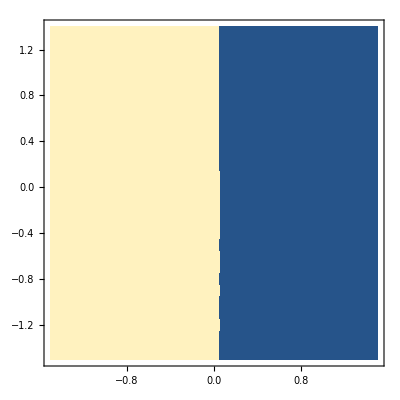

```mathematica
ListDensityPlot[points,PlotRange->All,InterpolationOrder->0]
```

```mathematica
points
```

{{-1.5,-1.5,1},{-1.5,-1.4,1},{-1.5,-1.3,1},{-1.4,-1.5,1},{-1.4,-1.4,1},{-1.4,-1.3,1},{-1.3,-1.5,1},{-1.3,-1.4,1},{-1.3,-1.3,1},{-1.2,-1.5,1},{-1.2,-1.4,1},{-1.2,-1.3,1},{-1.1,-1.5,1},{-1.1,-1.4,1},{-1.1,-1.3,1},{-1.,-1.5,1},{-1.,-1.4,1},{-1.,-1.3,1},{-0.9,-1.5,1},{-0.9,-1.4,1},{-0.9,-1.3,1},{-0.8,-1.5,1},{-0.8,-1.4,1},{-0.8,-1.3,1},{-0.7,-1.5,1},{-0.7,-1.4,1},{-0.7,-1.3,1},{-0.6,-1.5,1},{-0.6,-1.4,1},{-0.6,-1.3,1},{-0.5,-1.5,1},{-0.5,-1.4,1},{-0.5,-1.3,1},{-0.4,-1.5,1},{-0.4,-1.4,1},{-0.4,-1.3,1},{-0.3,-1.5,1},{-0.3,-1.4,1},{-0.3,-1.3,1},{-0.2,-1.5,1},{-0.2,-1.4,1},{-0.2,-1.3,1},{-0.1,-1.5,1},{-0.1,-1.4,1},{-0.1,-1.3,1},{0.,-1.5,1},{0.,-1.4,1},{0.,-1.3,1},{0.1,-1.5,-1},{0.1,-1.4,-1},{0.1,-1.3,-1},{0.2,-1.5,-1},{0.2,-1.4,-1},{0.2,-1.3,-1},{0.3,-1.5,-1},{0.3,-1.4,-1},{0.3,-1.3,-1},{0.4,-1.5,-1},{0.4,-1.4,-1},{0.4,-1.3,-1},{0.5,-1.5,-1},{0.5,-1.4,-1},{0.5,-1.3,-1},{0.6,-1.5,-1},{0.6,-1.4,-1},{0.6,-1.3,-1},{0.7,-1.5,-1},{0.7,-1.4,-1},{0.7,-1.3,-1},{0.8,-1.5,-1},{0.8,-1.4,-1},{0.8,-1.3,-1},{0.9,-1.5,-1},{0.9,-1.4,-1},{0.9,-1.3,-1},{1.,-1.5,-1},{1.,-1.4,-1},{1.,-1.3,-1},{1.1,-1.5,-1},{1.1,-1.4,-1},{1.1,-1.3,-1},{1.2,-1.5,-1},{1.2,-1.4,-1},{1.2,-1.3,-1},{1.3,-1.5,-1},{1.3,-1.4,-1},{1.3,-1.3,-1},{1.4,-1.5,-1},{1.4,-1.4,-1},{1.4,-1.3,-1},{1.5,-1.5,-1},{1.5,-1.4,-1},{1.5,-1.3,-1}}

```mathematica
Length[aaa]
```

31